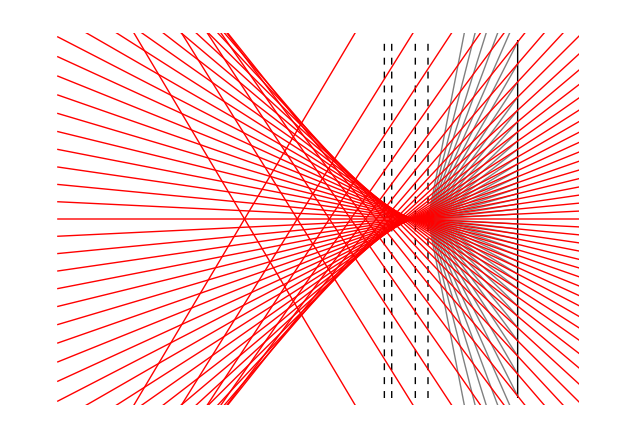

```mathematica
With[{nf=1.518,ni=1.33,na = 1.49,dcs=5,numθ=25,α=3.5,pry=10},
Block[{θi,θilist,θflist,αnp},
θi=ArcSin[na/nf];
θilist=Join[Table[θ,{θ,-θi,-θi/numθ,θi/numθ}],Table[θ,{θ,θi/numθ,θi,θi/numθ}]];
θflist=ArcSin[ni/nf Sin[#]]&/@θilist;
αnp=NIntegrate[(Tan[q]/Tan[ ArcSin[ni/nf Sin[q]]]),{q,0,ArcSin[na/nf]}]/ArcSin[na/nf];
Show[Graphics[{{{Thick,Line[{{0,-pry},{0,pry}}]},Dashed,Line[{{-dcs,-pry},{-dcs,pry}}],Line[{{-nf/ni dcs,-pry},{-nf/ni dcs,pry}}],Line[{{-(nf/ni)^3 dcs,-pry},{-(nf/ni)^3 dcs,pry}}],Line[{{-αnp dcs,-pry},{-αnp dcs,pry}}]},{Gray,Thin,Line[{{-dcs,0},{0,dcs Tan[#]}}]&/@θilist},
Thin,Red,Line[{{-(1+α)nf dcs/ni,0},{-(1-α)nf dcs/ni,0}}],Apply[Line[{{-(1+α)nf dcs/ni,dcs(Tan[#1]/Tan[#2]-(1-α)nf/ni)Tan[#2]-2α nf/ni dcs Tan[#2]},{-(1-α)nf dcs/ni,dcs(Tan[#1]/Tan[#2]-(1-α)nf/ni)Tan[#2]}}]&,Transpose[{θilist,θflist}],2]}
]
,PlotRange->{{-(1+α)nf dcs/ni,-(3-α)nf dcs/ni},{-pry,pry}}]
]]
```

```mathematica
Tan[ArcSin[θ]]
```

θ/(√(1-θ^2))

```mathematica
With[{nf=1.518,ni=1.33,na = 1.49,dcs=5,numθ=25,α=3.5,pry=10},
θm=ArcSin[na/nf];
θmlist=Join[Table[θ,{θ,-θm,-θm/numθ,θm/numθ}],Table[θ,{θ,θm/numθ,θm,θm/numθ}]];
θilist=ArcSin[ni/nf Sin[#]]&/@θmlist]
```

{-1.03525,-1.01495,-0.990562,-0.962587,-0.931501,-0.897742,-0.861699,-0.82371,-0.784065,-0.743012,-0.70076,-0.657485,-0.613338,-0.568446,-0.522917,-0.476845,-0.43031,-0.383381,-0.33612,-0.288582,-0.240816,-0.192865,-0.144771,-0.0965716,-0.0483029,0.0483029,0.0965716,0.144771,0.192865,0.240816,0.288582,0.33612,0.383381,0.43031,0.476845,0.522917,0.568446,0.613338,0.657485,0.70076,0.743012,0.784065,0.82371,0.861699,0.897742,0.931501,0.962587,0.990562,1.01495,1.03525}

```mathematica
θmlist
```

{-1.37843,-1.32329,-1.26816,-1.21302,-1.15788,-1.10274,-1.04761,-0.99247,-0.937333,-0.882196,-0.827058,-0.771921,-0.716784,-0.661647,-0.606509,-0.551372,-0.496235,-0.441098,-0.385961,-0.330823,-0.275686,-0.220549,-0.165412,-0.110274,-0.0551372,0.0551372,0.110274,0.165412,0.220549,0.275686,0.330823,0.385961,0.441098,0.496235,0.551372,0.606509,0.661647,0.716784,0.771921,0.827058,0.882196,0.937333,0.99247,1.04761,1.10274,1.15788,1.21302,1.26816,1.32329,1.37843}

```mathematica
abeW[u_]:=
```

```mathematica
w20 [nf_,ni_][u_]:=(2nf)/ni (ni-nf)(1-√(1-u^2))/2
w40[nf_,ni_][u_]:=(2 nf^2)/ni^3 (ni^2-nf^2)((1-√(1-u^2))/2)^2
def[nf_,zf_][u_]:=nf zf √(1-u^2)
```

```mathematica
Sin[θ/2]^2//TrigExpand
```

Sin[θ/2]^2

```mathematica
NIntegrate[(Tan[q]/Tan[ ArcSin[1.33/1.518Sin[q]]]),{q,0,ArcSin[1.4/1.52]}]/ArcSin[1.4/1.52]-1
```

0.261176

```mathematica
1.518/1.33-1
```

0.141353

```mathematica
With[{nf=1.518,ni=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=1.2,pry=2},
Manipulate[Plot[def[nf,zf][u]+w20 [nf,ni][u]+w40[nf,ni][u],{u,0,1.49/1.518}]
,{zf,-1,0}]]
```

```mathematica
D[def[nf,zf][u]+w20 [nf,ni][u]+w40[nf,ni][u],u]
```

(ni (-ni+nm) u)/(nm √(1-u^2))+(ni^2 (-ni^2+nm^2) u (1-√(1-u^2)))/(nm^3 √(1-u^2))-(ni u zf)/(√(1-u^2))

```mathematica
With[{nf=1.518,ni=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=1.2,pry=2},
Manipulate[Plot[(nf (-nf+ni) u)/(ni √(1-u^2))+(nf^2 (-nf^2+ni^2) u (1-√(1-u^2)))/(ni^3 √(1-u^2))-(nf u zf)/(√(1-u^2)),{u,0,1.49/1.518}]
,{zf,-1,0}]]
```

```mathematica
With[{nf=1.518,ni=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,pry=2},
Manipulate[Plot[{nf/ni √(1-(nf/ni u)^2)-α √(1-u^2),-(nf^3 u)/(ni^3 √(1-(nf^2 u^2)/ni^2))+(u α)/(√(1-u^2))},{u,0,ni/nf +0 1.49/1.518}]
,{α,1,2}]]
```

```mathematica
Integrate[nf/ni √(1-(nf/ni u)^2)-α √(1-u^2),{u,0,ni/nf}]
```

ConditionalExpression[1/4 (π-2 α ((nm √(1-nm^2/ni^2))/ni+ArcSin[nm/ni])), Re[ni/nm]>1||Re[ni/nm]<-1||ni/nm∉ℝ]

```mathematica
D[nf/ni √(1-(nf/ni u)^2)-α √(1-u^2),{u,1}]
```

-(ni^3 u)/(nm^3 √(1-(ni^2 u^2)/nm^2))+(u α)/(√(1-u^2))

```mathematica
With[{nf=1.518,ni=1.33},{nf/ni,nf^3/ni^3}]
```

{1.14135,1.48683}